```mathematica
-0.164414+2/(3r)+4/(3y)-x*(1/3)^(1/3)*y^(-4/3)
```

-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)

```mathematica
-(-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y))(r-y)^2
```

(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r-y)^2

```mathematica
Simplify[(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r-y)^2]
```

1/3 (0.493242-2/r+(3^(2/3) x)/y^(4/3)-4/y) (r-y)^2

```mathematica
Expand[1/3 (0.493242-2/r+(3^(2/3) x)/y^(4/3)-4/y) (r-y)^2]
```

2 r+0.164414 r^2+(r^2 x)/(3^(1/3) y^(4/3))-(4 r^2)/(3 y)-(2 r x)/(3^(1/3) y^(1/3))+(x y^(2/3))/3^(1/3)-0.328828 r y+0.164414 y^2-(2 y^2)/(3 r)

```mathematica
-(-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y))
```

0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)

```mathematica
(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y))(r+y)^2
```

(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r+y)^2

```mathematica
Simplify[(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r+y)^2]
```

1/3 (0.493242-2/r+(3^(2/3) x)/y^(4/3)-4/y) (r+y)^2

```mathematica
-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)
```

-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)

```mathematica
Simplify[-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)]
```

1/3 (-0.493242+2/r-(3^(2/3) x)/y^(4/3)+4/y)

```mathematica
Solve[-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)==0,x]
```

{{x→-1.44225 (0.164414-0.666667/r-1.33333/y) y^(4/3)}}

```mathematica
(-0.164414+2/(3 r)+4/(3 y))3^(1/3) y^(4/3)
```

```mathematica
(-0.164414+2/(3 r)+4/(3 y)) y^(4/3)
```

(-0.164414+2/(3 r)+4/(3 y)) y^(4/3)

```mathematica
(4/3)^(1/3)
```

2^(2/3)/3^(1/3)

```mathematica
N[2^(2/3)/3^(1/3)]
```

1.10064

```mathematica
NumberForm[1.100642416298209,16]
```

1.100642416298209

```mathematica
Grad[1/(√(a^2+r^2-2 a r Cos[θ])),{r,θ}]
```

{-(2 r-2 a Cos[θ])/(2 (a^2+r^2-2 a r Cos[θ])^(3/2)),-(a r Sin[θ])/((a^2+r^2-2 a r Cos[θ])^(3/2))}

```mathematica
(-(2 r-2 a Cos[θ])/(2 (a^2+r^2-2 a r Cos[θ])^(3/2)))^2+(-(a r Sin[θ])/((a^2+r^2-2 a r Cos[θ])^(3/2)))^2
```

(2 r-2 a Cos[θ])^2/(4 (a^2+r^2-2 a r Cos[θ])^3)+(a^2 r^2 Sin[θ]^2)/((a^2+r^2-2 a r Cos[θ])^3)

```mathematica
FullSimplify[(2 r-2 a Cos[θ])^2/(4 (a^2+r^2-2 a r Cos[θ])^3)+(a^2 r^2 Sin[θ]^2)/((a^2+r^2-2 a r Cos[θ])^3)]
```

((r-a Cos[θ])^2+a^2 r^2 Sin[θ]^2)/((a^2+r^2-2 a r Cos[θ])^3)

```mathematica
D[1/(√(a^2+r^2-2 a r Cos[θ])),r]
```

-(2 r-2 a Cos[θ])/(2 (a^2+r^2-2 a r Cos[θ])^(3/2))

```mathematica
D[1/(√(a^2+r^2-2 a r Cos[θ])),θ]
```

```mathematica
(-(a  Sin[θ])/((a^2+r^2-2 a r Cos[θ])^(3/2)))^2+(-(2 r-2 a Cos[θ])/(2 (a^2+r^2-2 a r Cos[θ])^(3/2)))^2
```

(2 r-2 a Cos[θ])^2/(4 (a^2+r^2-2 a r Cos[θ])^3)+(a^2 Sin[θ]^2)/((a^2+r^2-2 a r Cos[θ])^3)

```mathematica
Simplify[(2 r-2 a Cos[θ])^2/(4 (a^2+r^2-2 a r Cos[θ])^3)+(a^2 Sin[θ]^2)/((a^2+r^2-2 a r Cos[θ])^3)]
```

1/((a^2+r^2-2 a r Cos[θ])^2)

```mathematica
Subscript[n, 7][r_]=∫_({x,y}∈ImplicitRegion[2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)-0.164414≥0&&y≥0&&x∈Reals&&y∈Reals,{x,y}]) 1/r y AiryAi[x]*(2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)-0.164414)^2 *(Hypergeometric0F1[3,(x/(3^(1/3) y^(4/3))-2/(3 r)-4/(3 y)+0.164414) (r-y)^2]-Hypergeometric0F1[3,(x/(3^(1/3) y^(4/3))-2/(3 r)-4/(3 y)+0.164414) (r+y)^2])
```

∫_({x,y}∈ImplicitRegion[-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)≥0&&y≥0&&x∈ℝ&&y∈ℝ,{x,y}]) 1/r(-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y))^2 y AiryAi[x] (Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r-y)^2]-Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r+y)^2])

```mathematica
Subscript[n, 7][0.1]
```

41971.

```mathematica
Subscript[n, 7][0.05]
```

n_7[0.05]

```mathematica
Subscript[n, 7][0.01]
```

1.68114×10^7

```mathematica
Subscript[n, 7][0.005]
```

37.807

```mathematica
Subscript[n, 7][0.001]
```

8.83034×10^7

```mathematica
Subscript[n, 7][0.0005]
```

-2.27664×10^8

```mathematica
Subscript[n, 7][0.0001]
```

234.458

```mathematica
Subscript[n, 7][0.00005]
```

310.427

```mathematica
Subscript[n, 7][0.00001]
```

661.614

```mathematica
Table[Subscript[n, 7][r],{r,0.00001,0.00005,0.000001}]
```

16.6997

```mathematica
Subscript[n, 7][1]
```

∫_({x,y}∈ImplicitRegion[0.502253-x/(3^(1/3) y^(4/3))+4/(3 y)≥0&&y>0,{x,y}]) 1/3 (1.50676-(3^(2/3) x)/y^(4/3)+4/y) y AiryAi[x] (Hypergeometric0F1[3,1/3 (-1.50676+(3^(2/3) x)/y^(4/3)-4/y) (1-y)^2]-Hypergeometric0F1[3,1/3 (-1.50676+(3^(2/3) x)/y^(4/3)-4/y) (1+y)^2])

```mathematica
Subscript[N, 7][r_]=∫_({x,y}∈ImplicitRegion[ -0.164414+2/(3 r)-x/(3^(1/3)y^(4/3))+4/(3 y)≥0&&y>0&&x>0&&x∈Reals&&y∈Reals,{x,y}]) AiryAi[x](y/r) (-0.164414+2/(3 r)-x/(3^(1/3)y^(4/3))+4/(3 y))^2*(Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3)y^(4/3))-4/(3 y))(r-y)^2]-Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3)y^(4/3))-4/(3 y)) (r+y)^2])
```

∫_({x,y}∈ImplicitRegion[-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)≥0&&y>0&&x>0&&x∈ℝ&&y∈ℝ,{x,y}]) 1/r(-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y))^2 y AiryAi[x] (Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r-y)^2]-Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r+y)^2])

```mathematica
Subscript[N, 7][0.1]
```

21.7664-0.0000187214 ⅈ

```mathematica
Subscript[N, 7][0.05]
Subscript[N, 7][0.01]
Subscript[N, 7][0.005]
Subscript[N, 7][0.001]
Subscript[N, 7][0.0001]
```

47.8008

472.538

1309.07

14440.7

464544.

```mathematica
Simplify[%9]
```

1.69505×10^21

```mathematica
NSum[10. (6.502252666666666-x/(3^(1/3) y^(4/3))+4/(3 y))^2 y AiryAi[x] (BesselJ[2,2 √(6.502252666666666-x/(3^(1/3) y^(4/3))+4/(3 y)) (0.1-y)]/(0.1-y)^2-(0.1+y)^2 BesselJ[2,2 √(6.502252666666666-x/(3^(1/3) y^(4/3))+4/(3 y)) (0.1+y)]),{y,0,50,0.01},{x,-50,-1.4422495703074083 (-6.502252666666666-1.3333333333333333/y) y^(4/3),0.01}]
```

```mathematica
NSum[10. (6.502252666666666-x/(3^(1/3) y^(4/3))+4/(3 y))^2 y AiryAi[x] (BesselJ[2,2 √(6.502252666666666-x/(3^(1/3) y^(4/3))+4/(3 y)) (0.1-y)]/(0.1-y)^2-(0.1+y)^2 BesselJ[2,2 √(6.502252666666666-x/(3^(1/3) y^(4/3))+4/(3 y)) (0.1+y)]),{y,0,50,0.01},{x,-50,50,0.01}]
```

$Aborted

```mathematica
P[r_]=Integrate[AiryAi[x](y/r)(-0.164414+2/(3 r)-x/(3^(1/3) Max[y,0.005]^(4/3))+4/(3 Max[y,0.005]))^2(Hypergeometric0F1[3,-(√(-0.164414+2/(3 r)-x/(3^(1/3) Max[y,0.005]^(4/3))+4/(3 Max[y,0.005])))^2(r-y)]),{x,y}∈ImplicitRegion[-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)≥0&&y≥0,{x,y}]]
```

∫_({x,y}∈ImplicitRegion[-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)≥0&&y≥0,{x,y}]) (y AiryAi[x] Hypergeometric0F1[3,(r-y) (0.164414-2/(3 r)+x/(3^(1/3) Max[0.005,y]^(4/3))-4/(3 Max[0.005,y]))] (-0.164414+2/(3 r)-x/(3^(1/3) Max[0.005,y]^(4/3))+4/(3 Max[0.005,y]))^2)/r

```mathematica
∫_({x,y}∈ImplicitRegion[-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)≥0&&y≥0,{x,y}]) 1/r y AiryAi[x] (Hypergeometric0F1[3,(r-y) (0.164414-2/(3 r)+x/(3^(1/3) Max[0.005,y]^(4/3))-4/(3 Max[0.005,y]))]) (-0.164414+2/(3 r)-x/(3^(1/3) Max[0.005,y]^(4/3))+4/(3 Max[0.005,y]))^2
```

∫_({x,y}∈ImplicitRegion[-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)≥0&&y≥0,{x,y}]) (y AiryAi[x] Hypergeometric0F1[3,(r-y) (0.164414-2/(3 r)+x/(3^(1/3) Max[0.005,y]^(4/3))-4/(3 Max[0.005,y]))] (-0.164414+2/(3 r)-x/(3^(1/3) Max[0.005,y]^(4/3))+4/(3 Max[0.005,y]))^2)/r

```mathematica
P[0.1]
```

9.78941908499381×10^6695106

```mathematica
L(r_)=∫_({x,a,θ}∈ImplicitRegion[4/(3 √(a^2-2 a r cos(θ)+r^2))-x/(3^(1/3) (a^2-2 a r cos(θ)+r^2)^(2/3))+2/(3 r)-0.164414≥0∧a≥0∧0≤θ≤π,{x,a,θ}]) (sin(θ) x (4/(3 √(a^2-2 a r cos(θ)+r^2))-x/(3^(1/3) (a^2-2 a r cos(θ)+r^2)^(2/3))+2/(3 r)-0.164414)^(3/2) 32 a √(-x/(3^(1/3) (a^2-2 r cos(θ) a+r^2)^(2/3))+2/(3 r)+4/(3 √(a^2-2 r cos(θ) a+r^2))-0.164414))/(2 π^2 a)
```

∫_({x,a,θ}∈ImplicitRegion[-0.164414+2/(3 r)-x/(3^(1/3) (r^2-2 r Cos[θ] a+a^2)^(2/3))+4/(3 √(r^2-2 r Cos[θ] a+a^2))≥0.&&a≥0&&0≤θ≤π,{x,a,θ}]) (AiryAi[x] BesselJ[3,2 a √(-0.164414+2/(3 r)-x/(3^(1/3) (a^2+r^2-2 a r Cos[θ])^(2/3))+4/(3 √(a^2+r^2-2 a r Cos[θ])))] (-0.164414+2/(3 r)-x/(3^(1/3) (a^2+r^2-2 a r Cos[θ])^(2/3))+4/(3 √(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2)

```mathematica
L[0.1]
```

∫_({x,a,θ}∈ImplicitRegion[6.50225-x/(3^(1/3) (0.01-0.2 Cos[θ] a+a^2)^(2/3))+4/(3 √(0.01-0.2 Cos[θ] a+a^2))≥0.&&a≥0&&0≤θ≤π,{x,a,θ}]) (AiryAi[x] BesselJ[3,2 a √(6.50225-x/(3^(1/3) (0.01+a^2-0.2 a Cos[θ])^(2/3))+4/(3 √(0.01+a^2-0.2 a Cos[θ])))] (6.50225-x/(3^(1/3) (0.01+a^2-0.2 a Cos[θ])^(2/3))+4/(3 √(0.01+a^2-0.2 a Cos[θ])))^(3/2) Sin[θ])/(2 a π^2)

```mathematica
Simplify[%3]
```

∫_({x,a,θ}∈ImplicitRegion[6.50225-x/(3^(1/3) (0.01-0.2 Cos[θ] a+a^2)^(2/3))+4/(3 √(0.01-0.2 Cos[θ] a+a^2))≥0.&&a≥0&&0≤θ≤π,{x,a,θ}]) (AiryAi[x] BesselJ[3,2 a √(6.50225-x/(3^(1/3) (0.01+a^2-0.2 a Cos[θ])^(2/3))+4/(3 √(0.01+a^2-0.2 a Cos[θ])))] (6.50225-x/(3^(1/3) (0.01+a^2-0.2 a Cos[θ])^(2/3))+4/(3 √(0.01+a^2-0.2 a Cos[θ])))^(3/2) Sin[θ])/(2 a π^2)

```mathematica
Simplify[%11]
```

∫_({x,a,θ}∈ImplicitRegion[-0.164414+2/(3 0.1)+x/(3^(1/3) (a^2+0.1^2-2 a 0.1 Cos[θ])^(2/3))+4/(3 √(a^2+0.1^2-2 a 0.1 Cos[θ]))&&a≥0&&0≤θ≤π,{x,a,θ}]) (AiryAi[x] BesselJ[3,2 a √(6.50225+x/(3^(1/3) (0.01+a^2-0.2 a Cos[θ])^(2/3))+4/(3 √(0.01+a^2-0.2 a Cos[θ])))] (6.50225+x/(3^(1/3) (0.01+a^2-0.2 a Cos[θ])^(2/3))+4/(3 √(0.01+a^2-0.2 a Cos[θ])))^(3/2) Sin[θ])/(2 a π^2)

```mathematica
-0.164414+2/(3r)+4/(3 √(a^2+r^2-2 a r Cos[θ]))+x(1/3)^(1/3)1/((a^2+r^2-2 a r Cos[θ])^(2/3))
```

-0.164414+2/(3 r)+x/(3^(1/3) (a^2+r^2-2 a r Cos[θ])^(2/3))+4/(3 √(a^2+r^2-2 a r Cos[θ]))

```mathematica
∫_({a,θ}∈ImplicitRegion[-0.164414+2/(3 0.01)+x/(3^(1/3) (a^2+r^2-2 a 0.01 Cos[θ])^(2/3))+4/(3 √(a^2+0.01^2-2 a r Cos[θ]))&&a≥0&&0≤θ≤π,{x,a,θ}]) 1/(2 a π^2)AiryAi[x]BesselJ[3,2 a √(-0.164414+2/(3 0.01)+x/(3^(1/3) (a^2+r^2-2 a 0.01 Cos[θ])^(2/3))+4/(3 √(a^2+0.01^2-2 a r Cos[θ])))] (-0.164414+2/(3 0.01)+x/(3^(1/3) (a^2+r^2-2 a 0.01 Cos[θ])^(2/3))+4/(3 √(a^2+0.01^2-2 a r Cos[θ])))^(3/2) Sin[θ]
```

```mathematica
1/(2 a π^2)AiryAi[x]BesselJ[3,2 a √(-0.164414+2/(3 0.01)+x/(3^(1/3) (a^2+0.01^2-2 a 0.01 Cos[θ])^(2/3))+4/(3 √(a^2+0.01^2-2 a 0.01 Cos[θ])))] (-0.164414+2/(3 0.01)+x/(3^(1/3) (a^2+0.01^2-2 a 0.01 Cos[θ])^(2/3))+4/(3 √(a^2+0.01^2-2 a 0.01 Cos[θ])))^(3/2) Sin[θ]
```

1/(2 a π^2)AiryAi[x] BesselJ[3,2 a √(66.5023+x/(3^(1/3) (0.0001+a^2-0.02 a Cos[θ])^(2/3))+4/(3 √(0.0001+a^2-0.02 a Cos[θ])))] (66.5023+x/(3^(1/3) (0.0001+a^2-0.02 a Cos[θ])^(2/3))+4/(3 √(0.0001+a^2-0.02 a Cos[θ])))^(3/2) Sin[θ]

```mathematica
∫%17ⅆx
```

```mathematica
Manipulate[Plot[%17,{x,-80,8}],{a,0,8},{θ,0,Pi}]
```

```mathematica
Manipulate[Plot[%15,{x,-8,8}],{a,-8,8},{r,-2,2},{θ,-2,2}]
```

```mathematica
Manipulate[Plot[%13,{x,-8,8}],{a,0,8},{r,-2,2},{θ,-2,2}]
```

```mathematica
J[r_]=∫_({x,y}∈ImplicitRegion[0.5-(2 r^2)/3-(x y^(2/3))/3^(1/3)-(4 y^2)/3≥0&&y≥0,{x,y}]) AiryAi[x](y/r)(0.5-(2 r^2)/3-(x y^(2/3))/3^(1/3)-(4 y^2)/3)^2*(Hypergeometric0F1[3,-(0.5-(2 r^2)/3-(x y^(2/3))/3^(1/3)-(4 y^2)/3)(r-y)^2]-Hypergeometric0F1[3,-(0.5-(2 r^2)/3-(x y^(2/3))/3^(1/3)-(4 y^2)/3)(r+y)^2])
```

∫_({x,y}∈ImplicitRegion[0.5-(2 r^2)/3-(x y^(2/3))/3^(1/3)-(4 y^2)/3≥0&&y≥0,{x,y}]) 1/r y (0.5-(2 r^2)/3-(x y^(2/3))/3^(1/3)-(4 y^2)/3)^2 AiryAi[x] (Hypergeometric0F1[3,(r-y)^2 (-0.5+(2 r^2)/3+(x y^(2/3))/3^(1/3)+(4 y^2)/3)]-Hypergeometric0F1[3,(r+y)^2 (-0.5+(2 r^2)/3+(x y^(2/3))/3^(1/3)+(4 y^2)/3)])

```mathematica
J[0.1]
```

∫_({x,y}∈ImplicitRegion[0.493333-(x y^(2/3))/3^(1/3)-(4 y^2)/3≥0&&y≥0,{x,y}]) 10. y (0.493333-(x y^(2/3))/3^(1/3)-(4 y^2)/3)^2 AiryAi[x] (Hypergeometric0F1[3,(0.1-y)^2 (-0.493333+(x y^(2/3))/3^(1/3)+(4 y^2)/3)]-Hypergeometric0F1[3,(0.1+y)^2 (-0.493333+(x y^(2/3))/3^(1/3)+(4 y^2)/3)])

```mathematica
Y[r_]=∫_({x,y}∈ImplicitRegion[-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)≥0&&y>0,{x,y}]) AiryAi[x](y/r) (-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y))*(BesselJ[2,2 √(-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y))(r-y)](r-y)^-2-BesselJ[2,2 √(-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y))(r+y)](r+y)^-2)
```

∫_({x,y}∈ImplicitRegion[-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)≥0&&y>0,{x,y}]) ((-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)) y AiryAi[x] (BesselJ[2,2 √(-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)) (r-y)]/(r-y)^2-BesselJ[2,2 √(-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)) (r+y)]/(r+y)^2))/r

```mathematica
Y[0.1]
```

∫_({x,y}∈ImplicitRegion[6.50225-x/(3^(1/3) y^(4/3))+4/(3 y)≥0&&y>0,{x,y}]) 10. (6.50225-x/(3^(1/3) y^(4/3))+4/(3 y)) y AiryAi[x] (BesselJ[2,2 √(6.50225-x/(3^(1/3) y^(4/3))+4/(3 y)) (0.1-y)]/(0.1-y)^2-BesselJ[2,2 √(6.50225-x/(3^(1/3) y^(4/3))+4/(3 y)) (0.1+y)]/(0.1+y)^2)

```mathematica
T[r_]=Integrate[AiryAi[x](y/r) (-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y))^2*(Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y))(r-y)^2]-Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r+y)^2]) ,{y,0,Infinity},{x,-Infinity,-1.4422495703074083 (0.164414-0.6666666666666666/r-1.3333333333333333/y) y^(4/3)}]
```

$Aborted

```mathematica
Solve[-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)==0,x]
```

{{x→-1.44225 (0.164414-0.666667/r-1.33333/y) y^(4/3)}}

```mathematica
Hypergeometric0F1[3,x]
```

Hypergeometric0F1[3,x]

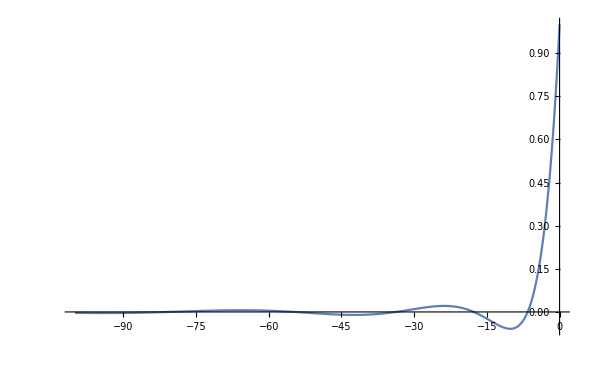

```mathematica
Plot[Hypergeometric0F1[3,x],{x,-100,0},PlotRange->All]
```

```mathematica
G[r_]=∫_({x,y}∈ImplicitRegion[-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)≥0&&y>0,{x,y}]) AiryAi[x] (-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y))^2*y*(Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y))(r-y)^2]-Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r+y)^2])
```

∫_({x,y}∈ImplicitRegion[-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)≥0&&y>0,{x,y}]) (-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y))^2 y AiryAi[x] (Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r-y)^2]-Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r+y)^2])

```mathematica
G[0.1]
```

4197.1

```mathematica
G[0.01]
```

63073.7

```mathematica
(-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y))^2 y AiryAi[x] (Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r-y)^2]-Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r+y)^2])
```

```mathematica
(-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y))^2 y AiryAi[x] (Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r-y)^2]-Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r+y)^2])/r
```

```mathematica
Manipulate[Plot[1/r(-0.164414+2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y))^2 y AiryAi[x] (Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r-y)^2]-Hypergeometric0F1[3,(0.164414-2/(3 r)+x/(3^(1/3) y^(4/3))-4/(3 y)) (r+y)^2]),{y,0,10}],{x,-100,50},{r,0,1}]
```

```mathematica
Manipulate[Plot[1/r(-0.164414+2/(3 r)+4/(3 y))^2 y AiryAi[0] (Hypergeometric0F1[3,(0.164414-2/(3 r)-4/(3 y)) (r-y)^2]-Hypergeometric0F1[3,(0.164414-2/(3 r)-4/(3 y)) (r+y)^2]),{r,0,1}],{y,0,10}]
```

```mathematica
Y[r_]=∫_({x,y}∈ImplicitRegion[5+2/3 r^2-(x y^(2/3))/3^(1/3)+4/3 y^2≥0&&y>0&&x∈Reals&&y∈Reals,{x,y}]) AiryAi[x](y/r) (5-2/3 r^2-(x y^(2/3))/3^(1/3)-4/3 y^2)^2*(Hypergeometric0F1[3,-(5-2/3 r^2-(x y^(2/3))/3^(1/3)-4/3 y^2)(r-y)^2]-Hypergeometric0F1[3,-(5-2/3 r^2-(x y^(2/3))/3^(1/3)-4/3 y^2) (r+y)^2])
```

$Aborted

```mathematica
Y[]
```

```mathematica
L[r_]=∫_({x,a,θ}∈ImplicitRegion[5-(2 r^2)/3-(x (a^2+r^2-2 a r Cos[θ])^(1/3))/3^(1/3)-4/3(a^2+r^2-2 a r Cos[θ])&&a≥0&&0≤θ≤π,{x,a,θ}]) 1/(2 a π^2)AiryAi[x]BesselJ[3,2 a √(5-(2 r^2)/3-(x (a^2+r^2-2 a r Cos[θ])^(1/3))/3^(1/3)-4/3(a^2+r^2-2 a r Cos[θ]))] (5-(2 r^2)/3-(x (a^2+r^2-2 a r Cos[θ])^(1/3))/3^(1/3)-4/3(a^2+r^2-2 a r Cos[θ]))^(3/2) Sin[θ]
```

```mathematica
L=∫_({x,a}∈ImplicitRegion[5-(x a^(2/3))/3^(1/3)-4/3 a^2≥0&&a≥0,{x,a}]) 1/(2 a π^2)AiryAi[x]BesselJ[3,2 a √(5-(x a^(2/3))/3^(1/3)-4/3 a^2)] ( 5-(x a^(2/3))/3^(1/3)-4/3 a^2)^(3/2)
```

∫_({x,a}∈ImplicitRegion[5-(x a^(2/3))/3^(1/3)-(4 a^2)/3≥0&&a≥0,{x,a}]) ((5-(4 a^2)/3-(a^(2/3) x)/3^(1/3))^(3/2) AiryAi[x] BesselJ[3,2 a √(5-(4 a^2)/3-(a^(2/3) x)/3^(1/3))])/(2 a π^2)

```mathematica
D[r/(√(a^2+r^2-2 a r Cos[θ])),r]
```

```mathematica
D[-(r (2 r-2 a Cos[θ]))/(2 (a^2+r^2-2 a r Cos[θ])^(3/2))+1/(√(a^2+r^2-2 a r Cos[θ])),r]
```

(3 r (2 r-2 a Cos[θ])^2)/(4 (a^2+r^2-2 a r Cos[θ])^(5/2))-r/((a^2+r^2-2 a r Cos[θ])^(3/2))-(2 r-2 a Cos[θ])/((a^2+r^2-2 a r Cos[θ])^(3/2))

```mathematica
Simplify[(3 r (2 r-2 a Cos[θ])^2)/(4 (a^2+r^2-2 a r Cos[θ])^(5/2))-r/((a^2+r^2-2 a r Cos[θ])^(3/2))-(2 r-2 a Cos[θ])/((a^2+r^2-2 a r Cos[θ])^(3/2))]
```

```mathematica
(a (4 (a^2+r^2) Cos[θ]-a r (7+Cos[2 θ])))/(2 (a^2+r^2-2 a r Cos[θ])^(5/2)r)
```

(a (4 (a^2+r^2) Cos[θ]-a r (7+Cos[2 θ])))/(2 r (a^2+r^2-2 a r Cos[θ])^(5/2))

```mathematica
D[1/(√(a^2+r^2-2 a r Cos[θ])),θ]
```

-(a r Sin[θ])/((a^2+r^2-2 a r Cos[θ])^(3/2))

```mathematica
D[-(a r Sin[θ])/((a^2+r^2-2 a r Cos[θ])^(3/2))*Sin[θ],θ]
```

```mathematica
-(2 a r Cos[θ] Sin[θ])/((a^2+r^2-2 a r Cos[θ])^(3/2))+(3 a^2 r^2 Sin[θ]^3)/((a^2+r^2-2 a r Cos[θ])^(5/2))
```

```mathematica
(-(2 a r Cos[θ] Sin[θ])/((a^2+r^2-2 a r Cos[θ])^(3/2))+(3 a^2 r^2 Sin[θ]^3)/((a^2+r^2-2 a r Cos[θ])^(5/2)))/(r^2 Sin[θ])
```

(Csc[θ] (-(2 a r Cos[θ] Sin[θ])/((a^2+r^2-2 a r Cos[θ])^(3/2))+(3 a^2 r^2 Sin[θ]^3)/((a^2+r^2-2 a r Cos[θ])^(5/2))))/r^2

```mathematica
Simplify[(Csc[θ] (-(2 a r Cos[θ] Sin[θ])/((a^2+r^2-2 a r Cos[θ])^(3/2))+(3 a^2 r^2 Sin[θ]^3)/((a^2+r^2-2 a r Cos[θ])^(5/2))))/r^2]
```

```mathematica
(a (-4 (a^2+r^2) Cos[θ]+a r (7+Cos[2 θ])))/(2 r (a^2+r^2-2 a r Cos[θ])^(5/2))+(a (4 (a^2+r^2) Cos[θ]-a r (7+Cos[2 θ])))/(2 r (a^2+r^2-2 a r Cos[θ])^(5/2))
```

(a (4 (a^2+r^2) Cos[θ]-a r (7+Cos[2 θ])))/(2 r (a^2+r^2-2 a r Cos[θ])^(5/2))+(a (-4 (a^2+r^2) Cos[θ]+a r (7+Cos[2 θ])))/(2 r (a^2+r^2-2 a r Cos[θ])^(5/2))

```mathematica
Simplify[(a (4 (a^2+r^2) Cos[θ]-a r (7+Cos[2 θ])))/(2 r (a^2+r^2-2 a r Cos[θ])^(5/2))+(a (-4 (a^2+r^2) Cos[θ]+a r (7+Cos[2 θ])))/(2 r (a^2+r^2-2 a r Cos[θ])^(5/2))]
```

0

```mathematica
J[r_]=∫_({x,y}∈ImplicitRegion[ -0.164414+2/(3 r)+4/(3 y)≥0&&y>0&&x∈Reals&&y∈Reals,{x,y}]) AiryAi[x](y/r) (-0.164414+2/(3 r)+4/(3 y))^2*(Hypergeometric0F1[3,(0.164414-2/(3 r)-4/(3 y))(r-y)^2]-Hypergeometric0F1[3,(0.164414-2/(3 r)-4/(3 y)) (r+y)^2])
```

∫_({x,y}∈ImplicitRegion[-0.164414+2/(3 r)+4/(3 y)≥0&&y>0&&x∈ℝ&&y∈ℝ,{x,y}]) ((-0.164414+2/(3 r)+4/(3 y))^2 y AiryAi[x] (Hypergeometric0F1[3,(0.164414-2/(3 r)-4/(3 y)) (r-y)^2]-Hypergeometric0F1[3,(0.164414-2/(3 r)-4/(3 y)) (r+y)^2]))/r

```mathematica
J[0.1]
```

105.908

```mathematica
J[0.05]
```

236.064

```mathematica
J[0.01]
```

1874.87

```mathematica
J[0.005]
```

4909.37

```mathematica
J[5]
```

0.290669

```mathematica
D[( a^2+r^2-2 a r Cos[θ])r,r]
```

```mathematica
Laplacian[( a^2+r^2-2 a r Cos[θ])^(-1/2),{r,θ,t},"Spherical"]
```

(3 (2 r-2 a Cos[θ])^2)/(4 (a^2+r^2-2 a r Cos[θ])^(5/2))-1/((a^2+r^2-2 a r Cos[θ])^(3/2))+(Csc[θ] (-(a Cos[θ] Sin[θ])/((a^2+r^2-2 a r Cos[θ])^(3/2))-((2 r-2 a Cos[θ]) Sin[θ])/(2 (a^2+r^2-2 a r Cos[θ])^(3/2))))/r+(-(a Cos[θ])/((a^2+r^2-2 a r Cos[θ])^(3/2))-(2 r-2 a Cos[θ])/(2 (a^2+r^2-2 a r Cos[θ])^(3/2))+(3 a^2 r Sin[θ]^2)/((a^2+r^2-2 a r Cos[θ])^(5/2)))/r

```mathematica
Simplify[%52]
```

0

```mathematica
Simplify[%50]
```

2/(√(a^2+r^2-2 a r Cos[θ]))

```mathematica
Laplacian[( a^2+r^2-2 a r Cos[θ]),{r,θ,t},"Spherical"]
```

4+(Csc[θ] (2 a Cos[θ] Sin[θ]+(2 r-2 a Cos[θ]) Sin[θ]))/r

```mathematica
Simplify[4+(Csc[θ] (2 a Cos[θ] Sin[θ]+(2 r-2 a Cos[θ]) Sin[θ]))/r]
```

6

```mathematica
Grad[a^2+r^2-2 a r Cos[θ],{a,θ,φ},"Spherical"]
```

{2 a-2 r Cos[θ],2 r Sin[θ],0}

```mathematica
(-(2 r-2 a Cos[θ])/(2 (a^2+r^2-2 a r Cos[θ])^(3/2)))^2+(-(a Sin[θ])/((a^2+r^2-2 a r Cos[θ])^(3/2)))^2
```

(2 r-2 a Cos[θ])^2/(4 (a^2+r^2-2 a r Cos[θ])^3)+(a^2 Sin[θ]^2)/((a^2+r^2-2 a r Cos[θ])^3)

```mathematica
Simplify[(2 r-2 a Cos[θ])^2/(4 (a^2+r^2-2 a r Cos[θ])^3)+(a^2 Sin[θ]^2)/((a^2+r^2-2 a r Cos[θ])^3)]
```

1/((a^2+r^2-2 a r Cos[θ])^2)

```mathematica
TrigReduce[1/((a^2+r^2-2 a r Cos[θ])^2)]
```

```mathematica
{-(2 a-2 r Cos[θ])/(2 (a^2+r^2-2 a r Cos[θ])^(3/2)),-(r Sin[θ])/((a^2+r^2-2 a r Cos[θ])^(3/2)),0}.{-(2 a-2 r Cos[θ])/(2 (a^2+r^2-2 a r Cos[θ])^(3/2)),-(r Sin[θ])/((a^2+r^2-2 a r Cos[θ])^(3/2)),0}
```

(2 a-2 r Cos[θ])^2/(4 (a^2+r^2-2 a r Cos[θ])^3)+(r^2 Sin[θ]^2)/((a^2+r^2-2 a r Cos[θ])^3)

```mathematica
Simplify[(2 a-2 r Cos[θ])^2/(4 (a^2+r^2-2 a r Cos[θ])^3)+(r^2 Sin[θ]^2)/((a^2+r^2-2 a r Cos[θ])^3)]
```

1/((a^2+r^2-2 a r Cos[θ])^2)

```mathematica
{2 a-2 r Cos[θ],2 r Sin[θ],0}.{2 a-2 r Cos[θ],2 r Sin[θ],0}
```

(2 a-2 r Cos[θ])^2+4 r^2 Sin[θ]^2

```mathematica
Simplify[(2 a-2 r Cos[θ])^2+4 r^2 Sin[θ]^2]
```

4 (a^2+r^2-2 a r Cos[θ])

```mathematica
J[r_]=∫_({x,y}∈ImplicitRegion[ 5-(2 r^2)/3-(4 y^2)/3-(2^(2/3)x (y^2)^(1/3))/3^(1/3)≥0&&y>0&&x∈Reals&&y∈Reals,{x,y}]) AiryAi[x](y/r) (5-(2 r^2)/3-(4 y^2)/3-(2^(2/3) x(y^2)^(1/3))/3^(1/3))^2(Hypergeometric0F1[3,(-5+(2 r^2)/3+(4 y^2)/3+(2^(2/3) x(y^2)^(1/3))/3^(1/3))(r-y)^2]-Hypergeometric0F1[3,(-5+(2 r^2)/3+(4 y^2)/3+(2^(2/3) x(y^2)^(1/3))/3^(1/3)) (r+y)^2])
```

$Aborted

```mathematica
J[0.1]
```

1.2916796750226848467369535450919757719805`15.954589770191005*^584307703021

```mathematica
J[0.05]
```

14.1046

```mathematica
J[0.01]
```

14.1475

```mathematica
J[0.5]
```

10.3106

```mathematica
J[3]
```

0

```mathematica
AiryAi[x](y/r) (-0.164414+2/(3 r)-2^(2/3)/3^(1/3)x/y^(4/3)+4/(3 y))^2*(Hypergeometric0F1[3,(0.164414-2/(3 r)+2^(2/3)/3^(1/3)x/(3^(1/3) y^(4/3))-4/(3 y))(r-y)^2]-Hypergeometric0F1[3,(0.164414-2/(3 r)+2^(2/3)/3^(1/3)x/(3^(1/3) y^(4/3))-4/(3 y)) (r+y)^2])
```

((-0.164414+2/(3 r)-(2^(2/3) x)/(3^(1/3) y^(4/3))+4/(3 y))^2 y AiryAi[x] (Hypergeometric0F1[3,(0.164414-2/(3 r)+((2/3)^(2/3) x)/y^(4/3)-4/(3 y)) (r-y)^2]-Hypergeometric0F1[3,(0.164414-2/(3 r)+((2/3)^(2/3) x)/y^(4/3)-4/(3 y)) (r+y)^2]))/r

```mathematica
Simplify[%10]
```

1/(r^3 y^(5/3))0.111111 (3.30193 r x+r (-4.+0.493242 y) y^(1/3)-2. y^(4/3))^2 AiryAi[x] (Hypergeometric0F1[3,(0.164414-2/(3 r)+(0.763143 x)/y^(4/3)-1.33333/y) (r-y)^2]-1. Hypergeometric0F1[3,(0.164414-2/(3 r)+(0.763143 x)/y^(4/3)-1.33333/y) (r+y)^2])

```mathematica
Manipulate[Plot[1/(r^3 y^(5/3))0.1111111111111111 (3.3019272488946263 r x+r (-4.+0.493242 y) y^(1/3)-2.0000000000000004 y^(4/3))^2 AiryAi[x] (Hypergeometric0F1[3,(0.164414-2/(3 r)+(0.7631428283688877 x)/y^(4/3)-1.3333333333333333/y) (r-y)^2]-1. Hypergeometric0F1[3,(0.164414-2/(3 r)+(0.7631428283688877 x)/y^(4/3)-1.3333333333333333/y) (r+y)^2]),{y,0,15},PlotRange->All],{r,0,1},{x,0,10}]
```

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/(3^(2/3) Gamma[2/3]) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Integrate[AiryAi[x] x^n,{x,-Infinity,Infinity}]
```

ConditionalExpression[3^(-1-n/3) ((3 Gamma[n])/Gamma[n/3]+(-3)^n (Gamma[(1+n)/3]/Gamma[1/3-n/3]+Gamma[(2+n)/3]/Gamma[2/3-n/3])),-1<Re[n]<3/4]

```mathematica
Manipulate[Plot[-(x^(1+n) (-3 Gamma[(1+n)/3] HypergeometricPFQRegularized[{(1+n)/3},{2/3,(4+n)/3},x^3/9]+3^(1/3) x Gamma[(2+n)/3] HypergeometricPFQRegularized[{(2+n)/3},{4/3,(5+n)/3},x^3/9]))/(9 3^(2/3)),{x,-10,100}],{n,0,10}]
```

```mathematica
AiryAiPrime[x]
```

AiryAiPrime[x]

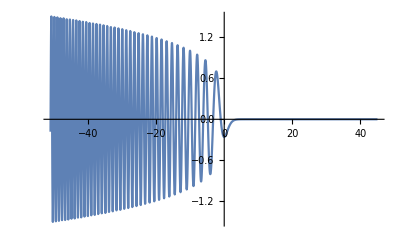

```mathematica
Plot[AiryAiPrime[x],{x,-51.,45.}]
```

```mathematica
AiryAi[x](y/r) (5-(2 r^2)/3-(4 y^2)/3-(2^(2/3) x(y^2)^(1/3))/3^(1/3))^2(Hypergeometric0F1[3,(-5+(2 r^2)/3+(4 y^2)/3+(2^(2/3) x(y^2)^(1/3))/3^(1/3))(r-y)^2]-Hypergeometric0F1[3,(-5+(2 r^2)/3+(4 y^2)/3+(2^(2/3) x(y^2)^(1/3))/3^(1/3)) (r+y)^2])
```

(y (5-(2 r^2)/3-(4 y^2)/3-(2^(2/3) x (y^2)^(1/3))/3^(1/3))^2 AiryAi[x] (Hypergeometric0F1[3,(r-y)^2 (-5+(2 r^2)/3+(4 y^2)/3+(2^(2/3) x (y^2)^(1/3))/3^(1/3))]-Hypergeometric0F1[3,(r+y)^2 (-5+(2 r^2)/3+(4 y^2)/3+(2^(2/3) x (y^2)^(1/3))/3^(1/3))]))/r

```mathematica
Manipulate[Plot[{(y (5-(2 r^2)/3-(4 y^2)/3-(2^(2/3) x (y^2)^(1/3))/3^(1/3))^2 AiryAi[x] (Hypergeometric0F1[3,(r-y)^2 (-5+(2 r^2)/3+(4 y^2)/3+(2^(2/3) x (y^2)^(1/3))/3^(1/3))]-Hypergeometric0F1[3,(r+y)^2 (-5+(2 r^2)/3+(4 y^2)/3+(2^(2/3) x (y^2)^(1/3))/3^(1/3))]))/r,(y (-5+2/(3r)+4/(3y)-x/(3^(1/3)y^(4/3)))^2 AiryAi[x] (Hypergeometric0F1[3,-(r-y)^2 (-5+2/(3r)+4/(3y)-x/(3^(1/3)y^(4/3)))]-Hypergeometric0F1[3,-(r+y)^2 (-5+2/(3r)+4/(3y)-x/(3^(1/3)y^(4/3)))]))/r,(2y (-5+2/(3r)+4/(3y)-x/(3^(1/3)y^(4/3))) AiryAi[x] (BesselJ[2,2(r-y) (-5+2/(3r)+4/(3y)-x/(3^(1/3)y^(4/3)))^(1/2)](r-y)^-2-BesselJ[2,2(r+y) (-5+2/(3r)+4/(3y)-x/(3^(1/3)y^(4/3)))^(1/2)](r+y)^-2))/r},{x,-80,20}],{r,0,2},{y,0,8}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression -1.52778+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression -1.52778+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Manipulate[Plot[{(y x (2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)-5)^2 (3-(r-y)^2 (-x/(3^(1/3) y^(4/3))+2/(3 r)+4/(3 y)-5)-3-(r+y)^2 (-x/(3^(1/3) y^(4/3))+2/(3 r)+4/(3 y)-5)))/r,(2 y x (2/(3 r)-x/(3^(1/3) y^(4/3))+4/(3 y)-5) ((22 Abs[r-y] √(-x/(3^(1/3) y^(4/3))+2/(3 r)+4/(3 y)-5))/(r-y)^2-(r+y)^-2 22 Abs[r+y] √(-x/(3^(1/3) y^(4/3))+2/(3 r)+4/(3 y)-5)))/r},{x,-80,20}],{r,0,2},{y,0,8}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression -5+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression -2.39583+ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression -2.39583+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Solve[-(x y^(2/3))/3^(1/3)-(2 r^2)/3-(4 y^2)/3+5==0,x]
```

{{x→1.44225 (-0.164414+0.666667/r+1.33333/y) y^(4/3)}}

```mathematica
x=(2/(3 r)+4/(3 y)-0.164414)3^(1/3) y^(4/3)
```

```mathematica
(-(2 r^2)/3-(4 y^2)/3+5)3^(1/3)/y^(2/3)==x
```

```mathematica
AiryAi[0]
```

1/(3^(2/3) Gamma[2/3])

```mathematica
N[1/(3^(2/3) Gamma[2/3])]
```

0.355028

```mathematica
2.4449537044620614*0.3550280538878173
```

0.868027

```mathematica
(2/(3 r)+4/(3 y)-0.164414)3^(1/3) y^(4/3)
```

3^(1/3) (-0.164414+2/(3 r)+4/(3 y)) y^(4/3)

```mathematica
Manipulate[Plot[3^(1/3) (-0.164414+2/(3 r)+4/(3 y)) y^(4/3),{y,0,0.01}],{r,0,0.01}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
(-(2 r^2)/3-(4 y^2)/3+5)3^(1/3)/y^(2/3)
```

(3^(1/3) (5-(2 r^2)/3-(4 y^2)/3))/y^(2/3)

```mathematica
Manipulate[Plot[(3^(1/3) (5-(2 r^2)/3-(4 y^2)/3))/y^(2/3),{y,0,10}],{r,0,0.1}]
```

```mathematica
AiryAi[x]
```

AiryAi[x]

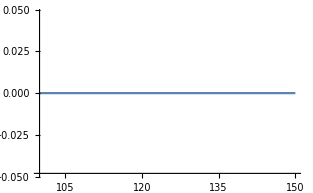

```mathematica
Plot[AiryAi[x],{x,100,150}]
```

```mathematica
Integrate[Exp[I(-a y^2)]Exp[I(b y)],{y,0,Infinity}]
```

ConditionalExpression[(ⅇ^((ⅈ b^2)/(4 a)) √π (1+Erf[(√(ⅈ a) b)/(2 a)]))/(2 √(ⅈ a)),(a∈ℝ&&Im[b]>0)||Im[a]<0]

```mathematica
Integrate[(ⅇ^((ⅈ b^2)/(4 a)) √π (1+Erf[(√(ⅈ a) Sin[u])/(2 a)]))/(2 √(ⅈ a))ⅇ^(ⅈ 3u),{u,-Pi,Pi}]
```

$Aborted

```mathematica
Integrate[Exp[I(-a y^2)]Exp[I(b y)],{y,0,Infinity}]
```